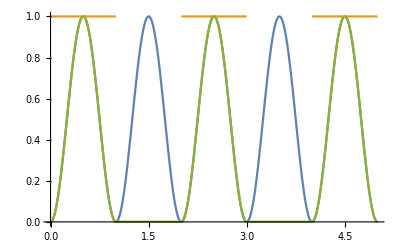

0.129449

```mathematica
Plot[{
Sin[π t]^2,
Mod[IntegerPart[t]+1,2],
Mod[IntegerPart[t]+1,2] Sin[π t]^2
},{t,0,5}]
```

{60,60.6852,61.3548,62.009,62.6483,63.273,63.8835,64.48,65.0629,65.6324,66.189,66.7328,67.2643,67.7835,68.291,68.7868,69.2713,69.7448,70.2074,70.6594,71.1012,71.5328,71.9546,72.3668,72.7695,73.1631,73.5476,73.9234,74.2906,74.6494,75.,75.3426,75.6774,76.0045,76.3242,76.6365,76.9417,77.24,77.5314,77.8162,78.0945,78.3664,78.6321,78.8918,79.1455,79.3934,79.6357,79.8724,80.1037,80.3297,80.5506,80.7664,80.9773,81.1834,81.3848,81.5815,81.7738,81.9617,82.1453,82.3247,82.5,82.6713,82.8387,83.0023,83.1621,83.3183,83.4709,83.62,83.7657,83.9081,84.0472,84.1832,84.3161,84.4459,84.5727,84.6967,84.8178,84.9362,85.0518,85.1649,85.2753}

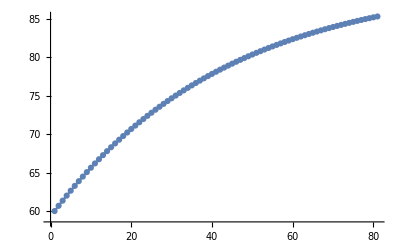

```mathematica
With[{a=1-Exp[-Log[2]0.05/1.50]},
NestList[#+a(90-#)&,60,80]
]
ListPlot[%,Joined->True,Mesh->All]
```

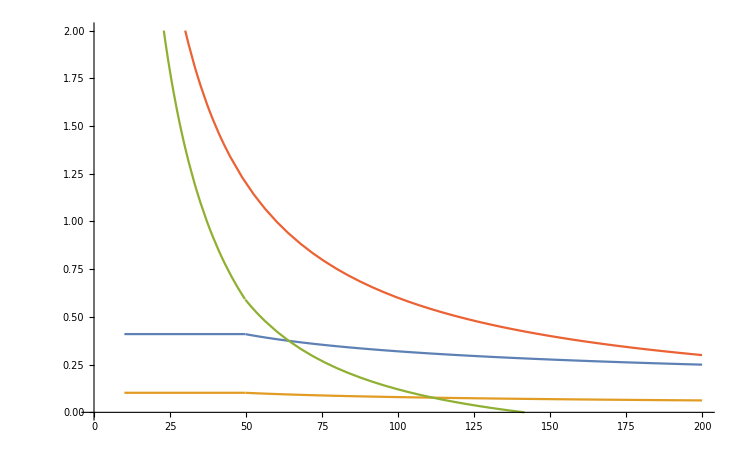

```mathematica
systole[p_]:=Min[7.4492(p 100)^0.3558/100,0.41]
Plot[Evaluate@With[{p=60/bpm},{
systole[p],
0.25systole[p],
p-1.5systole[p],
p
}],{bpm,10,200},PlotRange->{0,2}]
```

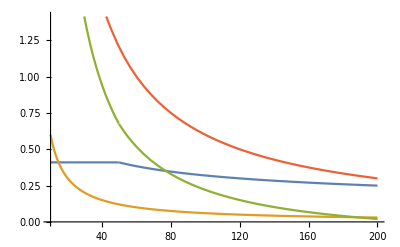

```mathematica
Plot[Evaluate@With[{p=60/bpm},{
systole[p],
0.10 60/bpm,
p-systole[p]-(0.10 60/bpm),
p
}],{bpm,10,200}]
```

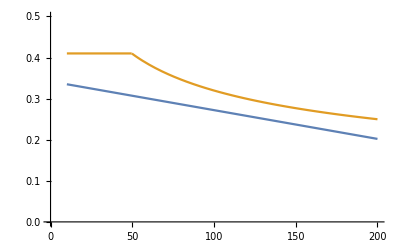

```mathematica
Plot[{
0.30-0.0007(bpm-60),
systole[60/bpm]
},{bpm,10,200},PlotRange->{0,0.5}]
```

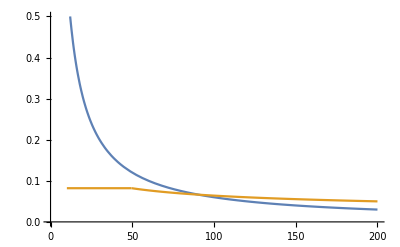

```mathematica
Plot[{
0.10 60/bpm,
0.2 systole[60/bpm]
},{bpm,10,200},PlotRange->{0,0.5}]
```

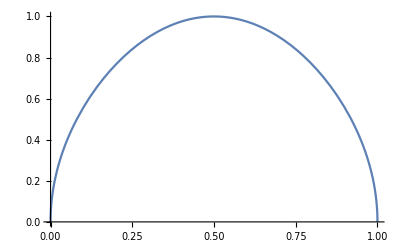

```mathematica
Plot[Sin[q π]^0.5,{q,0,1}]
```